```mathematica
releaseOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = 0;
attackMode = True;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: follow input exactly *)
attackMode = True;
output[[i]] = X[[i]],

(* release mode: set gradient to zero and start from last value *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False;ic1=0; ic2=prevY];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

prevY= output[[i]];
];

output
]


attackOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,prevY2,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: filter *)
(* if this is the first sample of the attack, switch to attack mode *)
If[!attackMode,
attackMode = True; ic1 = 0.5*(prevY-prevY2)*gInv; ic2 = prevY;
];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
,

(* release mode: copy input to output *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False];
output[[i]] = X[[i]];
];

prevY2 = prevY;
prevY= output[[i]];
];

output
]

qThreshold3[x_,h_]:=Module[{xx},xx=x-2h;
If[xx<-h,0,If[xx>h,xx,(xx+h)^2/(4h)]]]

ARTimeToCutoffFrequency[time_,numStages_]:=Module[{correctionFactor},correctionFactor=0.472859+0.434404*numStages;
1.0/(time/correctionFactor)]

EnvelopeProcessComplete[X_]:=Module[{numStages,Q,attackFc,releaseFc,sampleRate,output},
sampleRate = 48000;
numStages = 3;
attackFc =ARTimeToCutoffFrequency[1/200,numStages];
releaseFc = ARTimeToCutoffFrequency[1/2,numStages];
Q=0.5;

output =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFc ,Q,sampleRate],
releaseFc,Q,sampleRate],
releaseFc,Q,sampleRate],
attackFc,Q,sampleRate],
attackFc,Q,sampleRate],
attackFc,Q,sampleRate]; 


output
]

DSControlCurve[x_]:=1-(x-1)^2

DynamicSmoothing[X_,fc_,sensitivity_]:=Module[{i,sr,bandz,low1,low2,low1z,low2z,g0,gc,g,output},sr=48000;
gc=Tan[π fc/sr];
g0=2 gc/(1+gc);
output=X;
low1z=low2z=low1=low2=0;
(*For[i=1,i≤Length[X],i++,low1z=low1;
low2z=low2;
bandz=low2z-low1z;
g=Min[DSControlCurve[g0+sensitivity*Abs[bandz]],1.0];
low2=low2z+g*(low1z-low2z);
low1=N[low1z]+g*(X[[i]]-low1z);
output[[i]]=low2z;];*)For[i=1,i≤Length[X],i++,bandz=low2z-low1z;
g=Min[DSControlCurve[g0+sensitivity*Abs[bandz]],1.0];
low2z=low2z+g*(low1z-low2z);
low1z=N[low1z]+g*(X[[i]]-low1z);
output[[i]]=low2z;];
output]

ReleaseEnvelope[X_]:=Module[{numStages,Q,attackFc,releaseFcFast,releaseFcSlow,sampleRate,releaseFilteredSlow, releaseFilteredFast,output},
sampleRate = 48000;
numStages = 3;
attackFc =ARTimeToCutoffFrequency[1/9000,numStages];
releaseFcFast = ARTimeToCutoffFrequency[1/2,numStages];
releaseFcSlow = releaseFcFast / 10;
Q=0.5;

releaseFilteredFast =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFcFast,Q,sampleRate],
releaseFcFast,Q,sampleRate],
releaseFcFast,Q,sampleRate],
attackFc,Q,sampleRate],
attackFc,Q,sampleRate],
attackFc,Q,sampleRate]; 


releaseFilteredSlow =
releaseOnlySVF[
releaseFilteredFast,
releaseFcSlow,Q,sampleRate]; 

output = DynamicSmoothing[releaseFilteredSlow - releaseFilteredFast,1,2^(-3)];

{X,releaseFilteredSlow,releaseFilteredFast,releaseFilteredSlow - releaseFilteredFast ,output}
]

AttackEnvelope[X_]:=Module[{numStages,fMultiplier,Q,smoothingFc, attackSlowFc,releaseFc,sampleRate,attackFilteredSlow, attackFilteredFast,output, smoothedOutput},
sampleRate = 48000;
numStages = 3;
releaseFc = ARTimeToCutoffFrequency[1/2,numStages];
attackSlowFc = ARTimeToCutoffFrequency[1/10,numStages];
smoothingFc = ARTimeToCutoffFrequency[1/5,1];
Q=0.5;

attackFilteredFast =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
X,
releaseFc ,Q,sampleRate],
releaseFc ,Q,sampleRate],
releaseFc ,Q,sampleRate]; 

attackFilteredSlow =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
attackFilteredFast,
attackSlowFc ,Q,sampleRate],
attackSlowFc ,Q,sampleRate],
attackSlowFc ,Q,sampleRate]; 

output =(attackFilteredFast -attackFilteredSlow);

smoothedOutput = releaseOnlySVF[output,smoothingFc,Q,sampleRate];

{X,attackFilteredFast,attackFilteredSlow,output,smoothedOutput}
]

AfterAttackEnvelope[X_]:=Module[{fMultiplier,Q,attackFastFc, attackSlowFc,releaseFc,releaseFc2,sampleRate,attackFilteredSlow, attackFilteredFast,attackEnvSlowRelease,attackEnv},
sampleRate = 48000;
attackSlowFc = 10;
releaseFc = 15;
releaseFc2 = 3.5;
Q=0.5;
fMultiplier = 1.5;

attackFilteredFast =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate];

attackFilteredSlow =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
attackFilteredFast,
attackSlowFc fMultiplier,Q,sampleRate],
attackSlowFc fMultiplier,Q,sampleRate],
attackSlowFc fMultiplier,Q,sampleRate]; 

attackEnv =attackFilteredFast -attackFilteredSlow ;

attackEnvSlowRelease =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
attackEnv,
releaseFc2 fMultiplier,Q,sampleRate],
releaseFc2 fMultiplier,Q,sampleRate],
releaseFc2 fMultiplier,Q,sampleRate];

attackEnvSlowRelease -attackEnv
]

sampleRate = 48000;
length = 2^16;
input = Table[Sin[155 2 π N[x]]Sin[30 2π N[x]],{x,0,length/sampleRate,1/sampleRate}];
input[[2Round[Length[input]/4];;3Round[Length[input]/4]]]=0;

 ListLinePlot[ReleaseEnvelope[Abs[input]]] 

input = Table[ⅇ^(x) Sin[15 2π N[x]],{x,0,length/sampleRate,1/sampleRate}];
input[[2Round[Length[input]/4];;3Round[Length[input]/4]]]=0;

 ListLinePlot[ReleaseEnvelope[Abs[input]]] 

input = Table[ⅇ^(-x) Sin[15 2π N[x]],{x,0,length/sampleRate,1/sampleRate}];
input[[2Round[Length[input]/4];;3Round[Length[input]/4]]]=0;

 ListLinePlot[ReleaseEnvelope[Abs[input]]]
```

-Graphics-

-Graphics-

-Graphics-

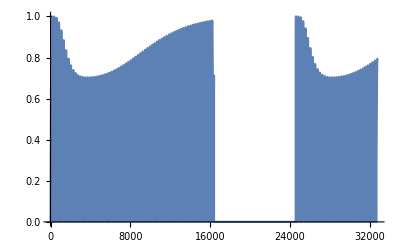

```mathematica
ListLinePlot[{Abs[input]*(1.0-0.3AfterAttackEnvelope[Abs[input]])}]
```

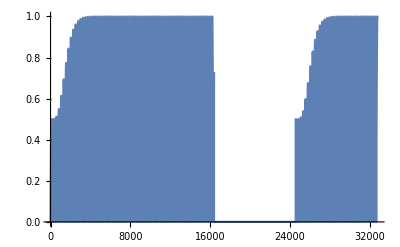

```mathematica
ListLinePlot[{(Abs[input](1.0 -0.5AttackEnvelope[Abs[input]]))},PlotRange->All]
```